```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,25000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[1,0.0001,1,0]
```

3.

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

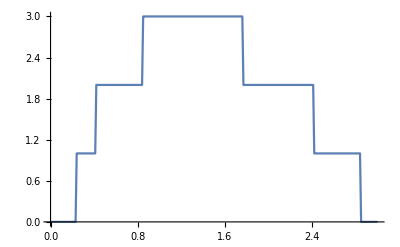

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,3,0.01]}]]
```

```mathematica
deltae3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}](*, μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)
tra:= Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
list={RandomSample[{imp,imp1,imp2,imp3}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.54085×10^-7},{0.01,2.44094×10^-7},{0.02,2.56907×10^-7},{0.03,2.71075×10^-7},{0.04,2.83092×10^-7},{0.05,2.94455×10^-7},{0.06,3.0694×10^-7},{0.07,3.2033×10^-7},{0.08,3.3717×10^-7},{0.09,3.57765×10^-7},{0.1,3.84407×10^-7},{0.11,4.15841×10^-7},{0.12,4.57222×10^-7},{0.13,5.07183×10^-7},{0.14,5.76398×10^-7},{0.15,6.66549×10^-7},{0.16,7.93696×10^-7},{0.17,9.78242×10^-7},{0.18,1.26559×10^-6},{0.19,1.75264×10^-6},{0.2,2.68637×10^-6},{0.21,4.91622×10^-6},{0.22,0.0000128906},{0.23,0.000118547},{0.24,0.38239},{0.25,0.650193},{0.26,0.76269},{0.27,0.82498},{0.28,0.860203},{0.29,0.885267},{0.3,0.905208},{0.31,0.915797},{0.32,0.923875},{0.33,0.928368},{0.34,0.930619},{0.35,0.930192},{0.36,0.930423},{0.37,0.926816},{0.38,0.917979},{0.39,0.901905},{0.4,0.867226},{0.41,0.738771},{0.42,0.963628},{0.43,1.37017},{0.44,1.54812},{0.45,1.64186},{0.46,1.7069},{0.47,1.74888},{0.48,1.77795},{0.49,1.80188},{0.5,1.82437},{0.51,1.83902},{0.52,1.84994},{0.53,1.86067},{0.54,1.86639},{0.55,1.872},{0.56,1.88114},{0.57,1.88704},{0.58,1.88984},{0.59,1.89443},{0.6,1.89555},{0.61,1.90112},{0.62,1.90304},{0.63,1.90203},{0.64,1.90805},{0.65,1.90791},{0.66,1.90934},{0.67,1.91166},{0.68,1.91201},{0.69,1.91305},{0.7,1.91298},{0.71,1.91168},{0.72,1.91287},{0.73,1.91221},{0.74,1.91389},{0.75,1.9132},{0.76,1.91188},{0.77,1.91096},{0.78,1.90775},{0.79,1.90414},{0.8,1.89697},{0.81,1.8893},{0.82,1.87458},{0.83,1.83814},{0.84,1.74554},{0.85,1.34404},{0.86,2.04935},{0.87,2.31065},{0.88,2.44289},{0.89,2.5417},{0.9,2.61495},{0.91,2.66724},{0.92,2.70233},{0.93,2.74006},{0.94,2.75826},{0.95,2.77688},{0.96,2.80048},{0.97,2.80993},{0.98,2.82943},{0.99,2.84118},{1.,2.84464},{1.01,2.85368},{1.02,2.8416},{1.03,2.78497},{1.04,2.61837},{1.05,2.1586},{1.06,1.53483},{1.07,1.52589},{1.08,1.90013},{1.09,2.17901},{1.1,2.35052},{1.11,2.43815},{1.12,2.5084},{1.13,2.55187},{1.14,2.58335},{1.15,2.61212},{1.16,2.63155},{1.17,2.64434},{1.18,2.65874},{1.19,2.66687},{1.2,2.67392},{1.21,2.68178},{1.22,2.68863},{1.23,2.69219},{1.24,2.69896},{1.25,2.70162},{1.26,2.70497},{1.27,2.70615},{1.28,2.70361},{1.29,2.70771},{1.3,2.70809},{1.31,2.70684},{1.32,2.70673},{1.33,2.71332},{1.34,2.7121},{1.35,2.70961},{1.36,2.70821},{1.37,2.70505},{1.38,2.70365},{1.39,2.70352},{1.4,2.70329},{1.41,2.70014},{1.42,2.69471},{1.43,2.69448},{1.44,2.69389},{1.45,2.68755},{1.46,2.68986},{1.47,2.68347},{1.48,2.68458},{1.49,2.67415},{1.5,2.67109},{1.51,2.66653},{1.52,2.65954},{1.53,2.65526},{1.54,2.64507},{1.55,2.63835},{1.56,2.64116},{1.57,2.62375},{1.58,2.61652},{1.59,2.6005},{1.6,2.58913},{1.61,2.58008},{1.62,2.5677},{1.63,2.55173},{1.64,2.53684},{1.65,2.52215},{1.66,2.49737},{1.67,2.47488},{1.68,2.44488},{1.69,2.40387},{1.7,2.35917},{1.71,2.31895},{1.72,2.2264},{1.73,2.1331},{1.74,1.9842},{1.75,1.74293},{1.76,1.15781},{1.77,1.29442},{1.78,1.22657},{1.79,1.28831},{1.8,1.21857},{1.81,1.3346},{1.82,1.47023},{1.83,1.60143},{1.84,1.68582},{1.85,1.73601},{1.86,1.76756},{1.87,1.78722},{1.88,1.80123},{1.89,1.81135},{1.9,1.81823},{1.91,1.82542},{1.92,1.82644},{1.93,1.83152},{1.94,1.83498},{1.95,1.83281},{1.96,1.83942},{1.97,1.83472},{1.98,1.83835},{1.99,1.8412},{2.,1.83891},{2.01,1.8387},{2.02,1.83714},{2.03,1.83821},{2.04,1.83831},{2.05,1.83838},{2.06,1.83284},{2.07,1.83459},{2.08,1.83416},{2.09,1.82978},{2.1,1.82826},{2.11,1.82741},{2.12,1.82727},{2.13,1.82139},{2.14,1.82117},{2.15,1.8148},{2.16,1.81463},{2.17,1.80993},{2.18,1.8094},{2.19,1.80053},{2.2,1.7978},{2.21,1.79847},{2.22,1.79187},{2.23,1.78747},{2.24,1.78347},{2.25,1.77773},{2.26,1.77014},{2.27,1.76198},{2.28,1.75029},{2.29,1.74},{2.3,1.73447},{2.31,1.71869},{2.32,1.70689},{2.33,1.68355},{2.34,1.66015},{2.35,1.63755},{2.36,1.60681},{2.37,1.57585},{2.38,1.53659},{2.39,1.45735},{2.4,1.32446},{2.41,0.942952},{2.42,0.626914},{2.43,0.66699},{2.44,0.692584},{2.45,0.689251},{2.46,0.706508},{2.47,0.780406},{2.48,0.814322},{2.49,0.853519},{2.5,0.870883},{2.51,0.880213},{2.52,0.891379},{2.53,0.898221},{2.54,0.898522},{2.55,0.899885},{2.56,0.903721},{2.57,0.905488},{2.58,0.906545},{2.59,0.904605},{2.6,0.90631},{2.61,0.903159},{2.62,0.900584},{2.63,0.904134},{2.64,0.90425},{2.65,0.906318},{2.66,0.900788},{2.67,0.900367},{2.68,0.8969},{2.69,0.895667},{2.7,0.893576},{2.71,0.88789},{2.72,0.880017},{2.73,0.872656},{2.74,0.871239},{2.75,0.859968},{2.76,0.845716},{2.77,0.835702},{2.78,0.827639},{2.79,0.799962},{2.8,0.79156},{2.81,0.777238},{2.82,0.76304},{2.83,0.713592},{2.84,0.55998},{2.85,0.000352264},{2.86,0.000015528},{2.87,4.85757×10^-6},{2.88,2.30045×10^-6},{2.89,1.32153×10^-6},{2.9,8.39509×10^-7},{2.91,5.83943×10^-7},{2.92,4.31898×10^-7},{2.93,3.38725×10^-7},{2.94,2.70201×10^-7},{2.95,2.22442×10^-7},{2.96,1.8491×10^-7},{2.97,1.55105×10^-7},{2.98,1.31006×10^-7},{2.99,1.1135×10^-7},{3.,9.70564×10^-8}}

```mathematica
Export["3imp.dat",%59]
```

3imp.dat

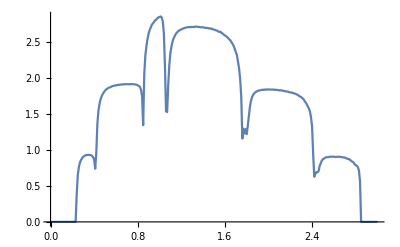

```mathematica
ListPlot[%59,Joined->True]
```

```mathematica
deltae4[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}](*,μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)
tra:= Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]],imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]]},
list={RandomSample[{imp4,imp1,imp2,imp3}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[{ω,Mean[Table[deltae4[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.62104×10^-7},{0.01,2.64044×10^-7},{0.02,2.73726×10^-7},{0.03,2.82249×10^-7},{0.04,2.91537×10^-7},{0.05,2.99971×10^-7},{0.06,3.10786×10^-7},{0.07,3.24419×10^-7},{0.08,3.40807×10^-7},{0.09,3.60553×10^-7},{0.1,3.86162×10^-7},{0.11,4.18106×10^-7},{0.12,4.57753×10^-7},{0.13,5.09849×10^-7},{0.14,5.77105×10^-7},{0.15,6.68349×10^-7},{0.16,7.94527×10^-7},{0.17,9.78744×10^-7},{0.18,1.2668×10^-6},{0.19,1.75481×10^-6},{0.2,2.69402×10^-6},{0.21,4.92344×10^-6},{0.22,0.0000129248},{0.23,0.000119605},{0.24,0.233372},{0.25,0.49993},{0.26,0.643201},{0.27,0.724697},{0.28,0.789195},{0.29,0.826743},{0.3,0.856546},{0.31,0.874783},{0.32,0.891751},{0.33,0.900455},{0.34,0.906797},{0.35,0.907062},{0.36,0.909519},{0.37,0.901598},{0.38,0.897115},{0.39,0.878567},{0.4,0.845239},{0.41,0.721331},{0.42,0.810898},{0.43,1.19498},{0.44,1.37853},{0.45,1.49782},{0.46,1.58014},{0.47,1.63916},{0.48,1.68703},{0.49,1.72078},{0.5,1.75762},{0.51,1.77227},{0.52,1.79463},{0.53,1.80842},{0.54,1.81944},{0.55,1.82997},{0.56,1.8427},{0.57,1.84959},{0.58,1.8535},{0.59,1.86334},{0.6,1.86618},{0.61,1.86928},{0.62,1.87341},{0.63,1.87553},{0.64,1.87805},{0.65,1.8832},{0.66,1.88351},{0.67,1.88303},{0.68,1.88397},{0.69,1.88676},{0.7,1.88501},{0.71,1.88755},{0.72,1.88692},{0.73,1.88421},{0.74,1.88749},{0.75,1.88604},{0.76,1.88573},{0.77,1.88213},{0.78,1.8804},{0.79,1.87715},{0.8,1.87034},{0.81,1.85892},{0.82,1.8416},{0.83,1.80272},{0.84,1.71342},{0.85,1.29785},{0.86,1.84192},{0.87,2.1065},{0.88,2.26975},{0.89,2.37526},{0.9,2.47535},{0.91,2.54047},{0.92,2.59154},{0.93,2.64128},{0.94,2.67623},{0.95,2.69931},{0.96,2.73555},{0.97,2.75455},{0.98,2.77402},{0.99,2.78875},{1.,2.80925},{1.01,2.81132},{1.02,2.79622},{1.03,2.72628},{1.04,2.51624},{1.05,1.94728},{1.06,1.27054},{1.07,1.23313},{1.08,1.65543},{1.09,1.97684},{1.1,2.16986},{1.11,2.29111},{1.12,2.36848},{1.13,2.42847},{1.14,2.47384},{1.15,2.50677},{1.16,2.52698},{1.17,2.54799},{1.18,2.55993},{1.19,2.57749},{1.2,2.58411},{1.21,2.59156},{1.22,2.60229},{1.23,2.60824},{1.24,2.61345},{1.25,2.61223},{1.26,2.61564},{1.27,2.61965},{1.28,2.62304},{1.29,2.62275},{1.3,2.62284},{1.31,2.62812},{1.32,2.62289},{1.33,2.6313},{1.34,2.62341},{1.35,2.62233},{1.36,2.61855},{1.37,2.61654},{1.38,2.61537},{1.39,2.61941},{1.4,2.61504},{1.41,2.6118},{1.42,2.61117},{1.43,2.59957},{1.44,2.59839},{1.45,2.59928},{1.46,2.59494},{1.47,2.58987},{1.48,2.58159},{1.49,2.58526},{1.5,2.58346},{1.51,2.57657},{1.52,2.56604},{1.53,2.55861},{1.54,2.54854},{1.55,2.54138},{1.56,2.53066},{1.57,2.51962},{1.58,2.51389},{1.59,2.49262},{1.6,2.48986},{1.61,2.47231},{1.62,2.45727},{1.63,2.43747},{1.64,2.41917},{1.65,2.39595},{1.66,2.37564},{1.67,2.35701},{1.68,2.3195},{1.69,2.27159},{1.7,2.23085},{1.71,2.16361},{1.72,2.09683},{1.73,1.9882},{1.74,1.83122},{1.75,1.56187},{1.76,1.06478},{1.77,1.37575},{1.78,1.16606},{1.79,1.17976},{1.8,1.09733},{1.81,1.16698},{1.82,1.25978},{1.83,1.3856},{1.84,1.55135},{1.85,1.63162},{1.86,1.67455},{1.87,1.70721},{1.88,1.7343},{1.89,1.7448},{1.9,1.75701},{1.91,1.7654},{1.92,1.77386},{1.93,1.77466},{1.94,1.77545},{1.95,1.78475},{1.96,1.78466},{1.97,1.78777},{1.98,1.78896},{1.99,1.79053},{2.,1.79119},{2.01,1.79422},{2.02,1.79082},{2.03,1.79295},{2.04,1.79551},{2.05,1.78887},{2.06,1.78576},{2.07,1.7898},{2.08,1.78556},{2.09,1.78236},{2.1,1.78261},{2.11,1.77945},{2.12,1.77933},{2.13,1.77106},{2.14,1.77067},{2.15,1.77043},{2.16,1.76281},{2.17,1.75689},{2.18,1.7601},{2.19,1.75166},{2.2,1.7452},{2.21,1.74562},{2.22,1.73429},{2.23,1.7316},{2.24,1.72204},{2.25,1.72358},{2.26,1.7172},{2.27,1.70381},{2.28,1.70084},{2.29,1.69399},{2.3,1.68411},{2.31,1.66907},{2.32,1.65404},{2.33,1.63322},{2.34,1.60747},{2.35,1.57977},{2.36,1.53368},{2.37,1.49816},{2.38,1.44785},{2.39,1.36677},{2.4,1.23301},{2.41,0.851676},{2.42,0.635357},{2.43,0.612084},{2.44,0.640635},{2.45,0.680931},{2.46,0.648278},{2.47,0.69307},{2.48,0.746232},{2.49,0.793103},{2.5,0.821882},{2.51,0.846938},{2.52,0.862127},{2.53,0.865057},{2.54,0.870534},{2.55,0.874276},{2.56,0.876664},{2.57,0.881448},{2.58,0.879632},{2.59,0.882083},{2.6,0.883204},{2.61,0.881947},{2.62,0.880205},{2.63,0.885566},{2.64,0.885578},{2.65,0.88359},{2.66,0.885684},{2.67,0.884949},{2.68,0.887075},{2.69,0.885344},{2.7,0.883576},{2.71,0.877605},{2.72,0.880184},{2.73,0.869529},{2.74,0.863762},{2.75,0.851994},{2.76,0.839606},{2.77,0.830119},{2.78,0.810798},{2.79,0.797421},{2.8,0.773571},{2.81,0.756739},{2.82,0.723717},{2.83,0.688904},{2.84,0.591629},{2.85,0.000445605},{2.86,0.0000159477},{2.87,4.92115×10^-6},{2.88,2.33716×10^-6},{2.89,1.36373×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Export["4imp.dat",%63]
```

4imp.dat

```mathematica
deltae5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{8,14}](*, μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)
tra:= Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1},{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]],imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]]},
list={RandomSample[{imp4,imp1,imp2,imp3}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[{ω,Mean[Table[deltae5[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.67936×10^-7},{0.01,2.70696×10^-7},{0.02,2.77118×10^-7},{0.03,2.8458×10^-7},{0.04,2.91578×10^-7},{0.05,3.00488×10^-7},{0.06,3.10707×10^-7},{0.07,3.24484×10^-7},{0.08,3.40612×10^-7},{0.09,3.61333×10^-7},{0.1,3.86236×10^-7},{0.11,4.18241×10^-7},{0.12,4.57825×10^-7},{0.13,5.0957×10^-7},{0.14,5.77112×10^-7},{0.15,6.68063×10^-7},{0.16,7.94286×10^-7},{0.17,9.80164×10^-7},{0.18,1.26763×10^-6},{0.19,1.75521×10^-6},{0.2,2.69402×10^-6},{0.21,4.92151×10^-6},{0.22,0.0000129274},{0.23,0.000119666},{0.24,0.156991},{0.25,0.378341},{0.26,0.52131},{0.27,0.627447},{0.28,0.702534},{0.29,0.751437},{0.3,0.80324},{0.31,0.828049},{0.32,0.84546},{0.33,0.862977},{0.34,0.875504},{0.35,0.883033},{0.36,0.881706},{0.37,0.877091},{0.38,0.873077},{0.39,0.854444},{0.4,0.820176},{0.41,0.707207},{0.42,0.742128},{0.43,1.04306},{0.44,1.24077},{0.45,1.36226},{0.46,1.45587},{0.47,1.53524},{0.48,1.58607},{0.49,1.63111},{0.5,1.668},{0.51,1.6997},{0.52,1.72397},{0.53,1.74473},{0.54,1.76481},{0.55,1.77764},{0.56,1.78875},{0.57,1.8025},{0.58,1.80916},{0.59,1.819},{0.6,1.82245},{0.61,1.83123},{0.62,1.83558},{0.63,1.84089},{0.64,1.84154},{0.65,1.84324},{0.66,1.84997},{0.67,1.85115},{0.68,1.85465},{0.69,1.85563},{0.7,1.85631},{0.71,1.85517},{0.72,1.8565},{0.73,1.85557},{0.74,1.85751},{0.75,1.85489},{0.76,1.85287},{0.77,1.85335},{0.78,1.84875},{0.79,1.84242},{0.8,1.83644},{0.81,1.82725},{0.82,1.80529},{0.83,1.77104},{0.84,1.67527},{0.85,1.32525},{0.86,1.71184},{0.87,1.93019},{0.88,2.0957},{0.89,2.22388},{0.9,2.31441},{0.91,2.39489},{0.92,2.45816},{0.93,2.51806},{0.94,2.5558},{0.95,2.60188},{0.96,2.63678},{0.97,2.66038},{0.98,2.68944},{0.99,2.70998},{1.,2.72218},{1.01,2.73436},{1.02,2.72219},{1.03,2.65724},{1.04,2.44463},{1.05,1.92146},{1.06,1.25732},{1.07,1.23526},{1.08,1.60298},{1.09,1.86646},{1.1,2.00149},{1.11,2.08766},{1.12,2.11442},{1.13,2.12947},{1.14,2.17524},{1.15,2.26445},{1.16,2.31443},{1.17,2.37515},{1.18,2.41301},{1.19,2.43431},{1.2,2.46194},{1.21,2.47992},{1.22,2.48418},{1.23,2.49932},{1.24,2.51649},{1.25,2.5198},{1.26,2.5267},{1.27,2.52969},{1.28,2.53371},{1.29,2.5433},{1.3,2.54265},{1.31,2.54637},{1.32,2.54688},{1.33,2.55493},{1.34,2.54977},{1.35,2.55248},{1.36,2.55229},{1.37,2.54359},{1.38,2.54457},{1.39,2.54167},{1.4,2.54497},{1.41,2.54725},{1.42,2.5369},{1.43,2.53653},{1.44,2.52905},{1.45,2.53148},{1.46,2.52829},{1.47,2.521},{1.48,2.51877},{1.49,2.51387},{1.5,2.50815},{1.51,2.49768},{1.52,2.49394},{1.53,2.48811},{1.54,2.47948},{1.55,2.46735},{1.56,2.45511},{1.57,2.45277},{1.58,2.43371},{1.59,2.42779},{1.6,2.41009},{1.61,2.39163},{1.62,2.3841},{1.63,2.35886},{1.64,2.34461},{1.65,2.32494},{1.66,2.29869},{1.67,2.26187},{1.68,2.24486},{1.69,2.18657},{1.7,2.1292},{1.71,2.0836},{1.72,1.98521},{1.73,1.88538},{1.74,1.73212},{1.75,1.50489},{1.76,1.02467},{1.77,1.37016},{1.78,1.27161},{1.79,1.13006},{1.8,1.13079},{1.81,1.12463},{1.82,1.10575},{1.83,1.22396},{1.84,1.32902},{1.85,1.46959},{1.86,1.56},{1.87,1.61593},{1.88,1.64709},{1.89,1.686},{1.9,1.71037},{1.91,1.72109},{1.92,1.73298},{1.93,1.73817},{1.94,1.74825},{1.95,1.75297},{1.96,1.75447},{1.97,1.75853},{1.98,1.76164},{1.99,1.76558},{2.,1.76212},{2.01,1.76542},{2.02,1.76697},{2.03,1.76527},{2.04,1.76663},{2.05,1.76409},{2.06,1.76584},{2.07,1.76489},{2.08,1.76662},{2.09,1.76364},{2.1,1.76161},{2.11,1.76299},{2.12,1.75874},{2.13,1.75166},{2.14,1.74955},{2.15,1.74898},{2.16,1.74279},{2.17,1.73625},{2.18,1.73248},{2.19,1.72842},{2.2,1.72072},{2.21,1.71845},{2.22,1.70745},{2.23,1.7099},{2.24,1.70047},{2.25,1.69931},{2.26,1.68669},{2.27,1.68544},{2.28,1.68541},{2.29,1.66163},{2.3,1.65137},{2.31,1.63147},{2.32,1.61103},{2.33,1.59976},{2.34,1.56155},{2.35,1.52369},{2.36,1.49163},{2.37,1.44028},{2.38,1.38112},{2.39,1.29866},{2.4,1.16021},{2.41,0.785089},{2.42,0.682853},{2.43,0.615641},{2.44,0.609279},{2.45,0.656132},{2.46,0.638531},{2.47,0.641976},{2.48,0.673548},{2.49,0.72626},{2.5,0.767431},{2.51,0.818081},{2.52,0.835144},{2.53,0.855643},{2.54,0.857572},{2.55,0.870243},{2.56,0.87445},{2.57,0.871485},{2.58,0.876631},{2.59,0.877661},{2.6,0.879752},{2.61,0.875988},{2.62,0.878065},{2.63,0.875286},{2.64,0.877988},{2.65,0.875817},{2.66,0.878161},{2.67,0.876139},{2.68,0.876521},{2.69,0.876887},{2.7,0.878762},{2.71,0.873555},{2.72,0.869643},{2.73,0.865826},{2.74,0.85211},{2.75,0.840267},{2.76,0.826367},{2.77,0.805642},{2.78,0.783642},{2.79,0.76043},{2.8,0.727782},{2.81,0.706931},{2.82,0.678778},{2.83,0.613599},{2.84,0.518781},{2.85,0.000471441},{2.86,0.0000162108},{2.87,4.9167×10^-6},{2.88,2.3327×10^-6},{2.89,1.36008×10^-6},{2.9,8.87196×10^-7},{2.91,6.22395×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Export["5imp.dat",%76]
```

5imp.dat

```mathematica
deltae6[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{8,14}], μ6=RandomInteger[{8,14}](*, μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)
tra:= Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1},{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]],imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]]},
list={RandomSample[{imp4,imp1,imp2,imp3}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[{ω,Mean[Table[deltae6[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.72255×10^-7},{0.01,2.74758×10^-7},{0.02,2.80099×10^-7},{0.03,2.8516×10^-7},{0.04,2.91585×10^-7},{0.05,2.99622×10^-7},{0.06,3.11712×10^-7},{0.07,3.24315×10^-7},{0.08,3.4094×10^-7},{0.09,3.61102×10^-7},{0.1,3.86818×10^-7},{0.11,4.18446×10^-7},{0.12,4.58598×10^-7},{0.13,5.09734×10^-7},{0.14,5.77438×10^-7},{0.15,6.68349×10^-7},{0.16,7.94795×10^-7},{0.17,9.803×10^-7},{0.18,1.26677×10^-6},{0.19,1.75532×10^-6},{0.2,2.69399×10^-6},{0.21,4.92475×10^-6},{0.22,0.0000129313},{0.23,0.000119966},{0.24,0.103054},{0.25,0.28695},{0.26,0.41548},{0.27,0.518502},{0.28,0.612659},{0.29,0.683127},{0.3,0.727637},{0.31,0.767581},{0.32,0.800602},{0.33,0.821622},{0.34,0.838006},{0.35,0.847522},{0.36,0.854967},{0.37,0.850779},{0.38,0.846579},{0.39,0.833076},{0.4,0.802161},{0.41,0.699657},{0.42,0.704142},{0.43,0.942345},{0.44,1.10851},{0.45,1.24726},{0.46,1.34186},{0.47,1.41968},{0.48,1.48838},{0.49,1.52829},{0.5,1.58967},{0.51,1.62203},{0.52,1.6516},{0.53,1.67756},{0.54,1.69999},{0.55,1.72286},{0.56,1.74086},{0.57,1.75436},{0.58,1.76381},{0.59,1.7806},{0.6,1.78592},{0.61,1.79567},{0.62,1.79523},{0.63,1.80541},{0.64,1.81076},{0.65,1.81641},{0.66,1.81777},{0.67,1.82166},{0.68,1.81925},{0.69,1.82947},{0.7,1.82541},{0.71,1.82553},{0.72,1.82561},{0.73,1.82637},{0.74,1.82714},{0.75,1.82874},{0.76,1.8269},{0.77,1.82255},{0.78,1.82087},{0.79,1.81487},{0.8,1.80929},{0.81,1.79335},{0.82,1.77643},{0.83,1.73927},{0.84,1.65387},{0.85,1.34113},{0.86,1.59014},{0.87,1.78835},{0.88,1.9416},{0.89,2.07034},{0.9,2.15072},{0.91,2.25027},{0.92,2.31608},{0.93,2.38617},{0.94,2.44157},{0.95,2.49326},{0.96,2.5329},{0.97,2.57243},{0.98,2.5991},{0.99,2.62539},{1.,2.65102},{1.01,2.66104},{1.02,2.65181},{1.03,2.58857},{1.04,2.38945},{1.05,1.87075},{1.06,1.27049},{1.07,1.20937},{1.08,1.54453},{1.09,1.76282},{1.1,1.82269},{1.11,1.88917},{1.12,1.88973},{1.13,1.87471},{1.14,1.92614},{1.15,2.02531},{1.16,2.13806},{1.17,2.22025},{1.18,2.25925},{1.19,2.31808},{1.2,2.34181},{1.21,2.36525},{1.22,2.3928},{1.23,2.40924},{1.24,2.42353},{1.25,2.43168},{1.26,2.43968},{1.27,2.45347},{1.28,2.4592},{1.29,2.46341},{1.3,2.45978},{1.31,2.47146},{1.32,2.46879},{1.33,2.47605},{1.34,2.47586},{1.35,2.4816},{1.36,2.4751},{1.37,2.47885},{1.38,2.47829},{1.39,2.46979},{1.4,2.48176},{1.41,2.47458},{1.42,2.46726},{1.43,2.46853},{1.44,2.45977},{1.45,2.45816},{1.46,2.45655},{1.47,2.45249},{1.48,2.44793},{1.49,2.44566},{1.5,2.44001},{1.51,2.429},{1.52,2.42335},{1.53,2.4234},{1.54,2.41869},{1.55,2.40226},{1.56,2.39427},{1.57,2.38811},{1.58,2.36735},{1.59,2.35859},{1.6,2.33443},{1.61,2.31688},{1.62,2.30294},{1.63,2.28987},{1.64,2.26466},{1.65,2.23913},{1.66,2.21286},{1.67,2.1879},{1.68,2.14665},{1.69,2.11072},{1.7,2.04609},{1.71,1.98425},{1.72,1.8982},{1.73,1.78646},{1.74,1.64403},{1.75,1.38574},{1.76,1.02629},{1.77,1.33339},{1.78,1.29739},{1.79,1.15659},{1.8,1.09801},{1.81,1.08798},{1.82,1.07837},{1.83,1.08787},{1.84,1.1806},{1.85,1.28107},{1.86,1.39185},{1.87,1.48156},{1.88,1.57421},{1.89,1.61941},{1.9,1.65091},{1.91,1.67015},{1.92,1.68632},{1.93,1.69952},{1.94,1.71202},{1.95,1.72126},{1.96,1.72383},{1.97,1.72715},{1.98,1.73638},{1.99,1.74042},{2.,1.73977},{2.01,1.73497},{2.02,1.74331},{2.03,1.74643},{2.04,1.74121},{2.05,1.74315},{2.06,1.74856},{2.07,1.74912},{2.08,1.74397},{2.09,1.7499},{2.1,1.74083},{2.11,1.74093},{2.12,1.73652},{2.13,1.73926},{2.14,1.73022},{2.15,1.72703},{2.16,1.72285},{2.17,1.71208},{2.18,1.71425},{2.19,1.7043},{2.2,1.69735},{2.21,1.70206},{2.22,1.69325},{2.23,1.68827},{2.24,1.67482},{2.25,1.66956},{2.26,1.66415},{2.27,1.65874},{2.28,1.64903},{2.29,1.63621},{2.3,1.62701},{2.31,1.6154},{2.32,1.58897},{2.33,1.56474},{2.34,1.53837},{2.35,1.51056},{2.36,1.45189},{2.37,1.40524},{2.38,1.33388},{2.39,1.25428},{2.4,1.10226},{2.41,0.744733},{2.42,0.737839},{2.43,0.649818},{2.44,0.610203},{2.45,0.622993},{2.46,0.634801},{2.47,0.632583},{2.48,0.636094},{2.49,0.679939},{2.5,0.709875},{2.51,0.756379},{2.52,0.799601},{2.53,0.834822},{2.54,0.849158},{2.55,0.857333},{2.56,0.864324},{2.57,0.871255},{2.58,0.874021},{2.59,0.87264},{2.6,0.877869},{2.61,0.872967},{2.62,0.875429},{2.63,0.873823},{2.64,0.874828},{2.65,0.875664},{2.66,0.872499},{2.67,0.872912},{2.68,0.871765},{2.69,0.87012},{2.7,0.874254},{2.71,0.871357},{2.72,0.869423},{2.73,0.863316},{2.74,0.85092},{2.75,0.841906},{2.76,0.825848},{2.77,0.807708},{2.78,0.777461},{2.79,0.752343},{2.8,0.708518},{2.81,0.671213},{2.82,0.621952},{2.83,0.562873},{2.84,0.435227},{2.85,0.000486005},{2.86,0.0000163941},{2.87,4.93647×10^-6},{2.88,2.3403×10^-6},{2.89,1.36027×10^-6},{2.9,8.85554×10^-7},{2.91,6.22049×10^-7},{2.92,4.60535×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Export["6imp.dat",%67]
```

6imp.dat

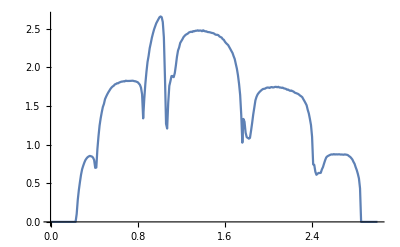

```mathematica
ListPlot[%67,Joined->True]
```

```mathematica
deltae7[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{8,14}], μ6=RandomInteger[{8,14}], μ7=RandomInteger[{8,14}](*,μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)
tra:= Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1},{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]],imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]]},
list={RandomSample[{imp4,imp1,imp2,imp3}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[{ω,Mean[Table[deltae7[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.73975×10^-7},{0.01,2.76683×10^-7},{0.02,2.81948×10^-7},{0.03,2.86685×10^-7},{0.04,2.91892×10^-7},{0.05,3.00693×10^-7},{0.06,3.11356×10^-7},{0.07,3.25031×10^-7},{0.08,3.41228×10^-7},{0.09,3.61327×10^-7},{0.1,3.86812×10^-7},{0.11,4.18512×10^-7},{0.12,4.58428×10^-7},{0.13,5.10023×10^-7},{0.14,5.77138×10^-7},{0.15,6.68222×10^-7},{0.16,7.94975×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75539×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129387},{0.23,0.000119885},{0.24,0.0707008},{0.25,0.204958},{0.26,0.32113},{0.27,0.428608},{0.28,0.513177},{0.29,0.596939},{0.3,0.654971},{0.31,0.708707},{0.32,0.738617},{0.33,0.773891},{0.34,0.80202},{0.35,0.818194},{0.36,0.828555},{0.37,0.830835},{0.38,0.82445},{0.39,0.816396},{0.4,0.783826},{0.41,0.700519},{0.42,0.682144},{0.43,0.857598},{0.44,1.00134},{0.45,1.12826},{0.46,1.22165},{0.47,1.31165},{0.48,1.38537},{0.49,1.44176},{0.5,1.491},{0.51,1.54872},{0.52,1.57459},{0.53,1.61113},{0.54,1.64167},{0.55,1.67026},{0.56,1.68613},{0.57,1.7039},{0.58,1.71878},{0.59,1.73575},{0.6,1.74909},{0.61,1.75625},{0.62,1.76669},{0.63,1.77078},{0.64,1.77918},{0.65,1.7837},{0.66,1.78421},{0.67,1.79433},{0.68,1.79319},{0.69,1.79835},{0.7,1.80039},{0.71,1.80217},{0.72,1.80077},{0.73,1.8019},{0.74,1.80258},{0.75,1.79797},{0.76,1.79685},{0.77,1.79838},{0.78,1.7904},{0.79,1.79062},{0.8,1.77739},{0.81,1.76584},{0.82,1.74723},{0.83,1.70438},{0.84,1.63543},{0.85,1.32954},{0.86,1.54744},{0.87,1.70009},{0.88,1.8189},{0.89,1.94206},{0.9,2.02356},{0.91,2.1145},{0.92,2.19789},{0.93,2.26683},{0.94,2.33408},{0.95,2.39535},{0.96,2.44317},{0.97,2.4758},{0.98,2.53101},{0.99,2.55793},{1.,2.5763},{1.01,2.59439},{1.02,2.58366},{1.03,2.52771},{1.04,2.3322},{1.05,1.85271},{1.06,1.24638},{1.07,1.2085},{1.08,1.50509},{1.09,1.66977},{1.1,1.69859},{1.11,1.72627},{1.12,1.68347},{1.13,1.64751},{1.14,1.71341},{1.15,1.85285},{1.16,1.97391},{1.17,2.08305},{1.18,2.13931},{1.19,2.20372},{1.2,2.244},{1.21,2.27478},{1.22,2.29354},{1.23,2.31604},{1.24,2.33712},{1.25,2.35349},{1.26,2.36281},{1.27,2.37274},{1.28,2.37442},{1.29,2.38762},{1.3,2.39646},{1.31,2.40772},{1.32,2.40244},{1.33,2.40437},{1.34,2.4077},{1.35,2.41402},{1.36,2.41415},{1.37,2.40677},{1.38,2.40907},{1.39,2.41747},{1.4,2.41078},{1.41,2.4054},{1.42,2.40272},{1.43,2.40167},{1.44,2.40335},{1.45,2.39905},{1.46,2.39376},{1.47,2.38652},{1.48,2.38303},{1.49,2.37728},{1.5,2.38087},{1.51,2.36789},{1.52,2.36008},{1.53,2.36079},{1.54,2.35227},{1.55,2.34124},{1.56,2.32822},{1.57,2.32484},{1.58,2.29965},{1.59,2.29173},{1.6,2.27899},{1.61,2.2594},{1.62,2.23041},{1.63,2.21424},{1.64,2.18943},{1.65,2.16424},{1.66,2.1407},{1.67,2.11341},{1.68,2.08307},{1.69,2.03201},{1.7,1.98221},{1.71,1.90671},{1.72,1.81186},{1.73,1.70161},{1.74,1.56389},{1.75,1.33619},{1.76,1.02248},{1.77,1.25303},{1.78,1.28492},{1.79,1.21228},{1.8,1.09577},{1.81,1.05613},{1.82,1.02995},{1.83,1.02886},{1.84,1.06724},{1.85,1.1334},{1.86,1.24493},{1.87,1.3606},{1.88,1.46388},{1.89,1.54549},{1.9,1.57817},{1.91,1.6196},{1.92,1.64867},{1.93,1.66268},{1.94,1.67791},{1.95,1.69694},{1.96,1.70206},{1.97,1.70668},{1.98,1.70574},{1.99,1.706},{2.,1.71354},{2.01,1.7196},{2.02,1.7244},{2.03,1.72309},{2.04,1.72754},{2.05,1.72255},{2.06,1.72798},{2.07,1.72339},{2.08,1.72632},{2.09,1.72056},{2.1,1.72422},{2.11,1.72201},{2.12,1.71823},{2.13,1.71728},{2.14,1.71904},{2.15,1.70954},{2.16,1.70299},{2.17,1.70342},{2.18,1.69682},{2.19,1.69184},{2.2,1.68686},{2.21,1.67548},{2.22,1.66916},{2.23,1.66473},{2.24,1.65689},{2.25,1.64903},{2.26,1.64352},{2.27,1.6394},{2.28,1.62743},{2.29,1.62367},{2.3,1.61537},{2.31,1.5925},{2.32,1.56922},{2.33,1.55764},{2.34,1.51027},{2.35,1.49663},{2.36,1.4337},{2.37,1.37878},{2.38,1.30858},{2.39,1.20823},{2.4,1.06116},{2.41,0.713355},{2.42,0.737305},{2.43,0.704471},{2.44,0.620454},{2.45,0.594703},{2.46,0.596633},{2.47,0.604459},{2.48,0.60994},{2.49,0.631514},{2.5,0.656044},{2.51,0.710983},{2.52,0.763446},{2.53,0.792202},{2.54,0.831174},{2.55,0.849462},{2.56,0.855416},{2.57,0.86794},{2.58,0.871136},{2.59,0.87527},{2.6,0.872636},{2.61,0.870954},{2.62,0.870787},{2.63,0.872159},{2.64,0.872532},{2.65,0.872197},{2.66,0.868175},{2.67,0.867703},{2.68,0.869238},{2.69,0.868745},{2.7,0.874082},{2.71,0.876757},{2.72,0.872479},{2.73,0.869453},{2.74,0.861014},{2.75,0.855367},{2.76,0.835546},{2.77,0.81112},{2.78,0.790135},{2.79,0.756713},{2.8,0.703071},{2.81,0.65922},{2.82,0.592219},{2.83,0.50902},{2.84,0.379849},{2.85,0.00048988},{2.86,0.0000164378},{2.87,4.96164×10^-6},{2.88,2.34886×10^-6},{2.89,1.3593×10^-6},{2.9,8.85307×10^-7},{2.91,6.22444×10^-7},{2.92,4.60317×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Export["7imp.dat",%68]
```

7imp.dat

```mathematica
deltae8[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{8,14}], μ6=RandomInteger[{8,14}], μ7=RandomInteger[{8,14}],μ8=RandomInteger[{8,14}](*, μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)
tra:= Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1},{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]],imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4},{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]]},
list={RandomSample[{imp4,imp1,imp2,imp3}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Table[{ω,Mean[Table[deltae8[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.76472×10^-7},{0.01,2.79563×10^-7},{0.02,2.82177×10^-7},{0.03,2.87108×10^-7},{0.04,2.93018×10^-7},{0.05,3.0118×10^-7},{0.06,3.11792×10^-7},{0.07,3.24907×10^-7},{0.08,3.41328×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18457×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92494×10^-6},{0.22,0.0000129427},{0.23,0.000119868},{0.24,0.050598},{0.25,0.150229},{0.26,0.257246},{0.27,0.347901},{0.28,0.438896},{0.29,0.515325},{0.3,0.584011},{0.31,0.630855},{0.32,0.69277},{0.33,0.721901},{0.34,0.757182},{0.35,0.778904},{0.36,0.787597},{0.37,0.79698},{0.38,0.803517},{0.39,0.791396},{0.4,0.763086},{0.41,0.682966},{0.42,0.657228},{0.43,0.805133},{0.44,0.937654},{0.45,1.03407},{0.46,1.1348},{0.47,1.2115},{0.48,1.28818},{0.49,1.35184},{0.5,1.40916},{0.51,1.45982},{0.52,1.50136},{0.53,1.52577},{0.54,1.58297},{0.55,1.60348},{0.56,1.63012},{0.57,1.644},{0.58,1.66857},{0.59,1.68706},{0.6,1.7081},{0.61,1.71903},{0.62,1.72444},{0.63,1.73813},{0.64,1.744},{0.65,1.75657},{0.66,1.75356},{0.67,1.76487},{0.68,1.76784},{0.69,1.76778},{0.7,1.7697},{0.71,1.777},{0.72,1.77308},{0.73,1.77798},{0.74,1.77284},{0.75,1.77154},{0.76,1.77686},{0.77,1.76699},{0.78,1.76782},{0.79,1.75795},{0.8,1.75189},{0.81,1.74094},{0.82,1.71615},{0.83,1.68036},{0.84,1.60519},{0.85,1.36418},{0.86,1.49668},{0.87,1.62411},{0.88,1.72871},{0.89,1.81926},{0.9,1.92349},{0.91,1.98892},{0.92,2.08627},{0.93,2.15122},{0.94,2.2101},{0.95,2.288},{0.96,2.33178},{0.97,2.39639},{0.98,2.43169},{0.99,2.47931},{1.,2.50566},{1.01,2.52863},{1.02,2.52575},{1.03,2.47342},{1.04,2.27621},{1.05,1.82861},{1.06,1.23364},{1.07,1.21342},{1.08,1.43688},{1.09,1.5545},{1.1,1.56},{1.11,1.56795},{1.12,1.52008},{1.13,1.44097},{1.14,1.53332},{1.15,1.68801},{1.16,1.83854},{1.17,1.95064},{1.18,2.01696},{1.19,2.0991},{1.2,2.13829},{1.21,2.18122},{1.22,2.21799},{1.23,2.23562},{1.24,2.26235},{1.25,2.2682},{1.26,2.29345},{1.27,2.29773},{1.28,2.31023},{1.29,2.31424},{1.3,2.32722},{1.31,2.3301},{1.32,2.33814},{1.33,2.34168},{1.34,2.33812},{1.35,2.35268},{1.36,2.3518},{1.37,2.35598},{1.38,2.35764},{1.39,2.35966},{1.4,2.34658},{1.41,2.34727},{1.42,2.35048},{1.43,2.33532},{1.44,2.34173},{1.45,2.32917},{1.46,2.32815},{1.47,2.33138},{1.48,2.32436},{1.49,2.31839},{1.5,2.31801},{1.51,2.31141},{1.52,2.30551},{1.53,2.30599},{1.54,2.29406},{1.55,2.27724},{1.56,2.27272},{1.57,2.27668},{1.58,2.24231},{1.59,2.22503},{1.6,2.20415},{1.61,2.19037},{1.62,2.17194},{1.63,2.15257},{1.64,2.12192},{1.65,2.09968},{1.66,2.06538},{1.67,2.03436},{1.68,2.00334},{1.69,1.968},{1.7,1.89982},{1.71,1.84738},{1.72,1.75334},{1.73,1.62017},{1.74,1.47416},{1.75,1.26656},{1.76,0.999445},{1.77,1.17046},{1.78,1.27599},{1.79,1.24341},{1.8,1.16729},{1.81,1.07334},{1.82,0.998296},{1.83,0.990029},{1.84,0.988158},{1.85,1.00756},{1.86,1.09964},{1.87,1.23195},{1.88,1.334},{1.89,1.44508},{1.9,1.53006},{1.91,1.57225},{1.92,1.60394},{1.93,1.63333},{1.94,1.63503},{1.95,1.64878},{1.96,1.66276},{1.97,1.67009},{1.98,1.68041},{1.99,1.68447},{2.,1.69622},{2.01,1.69446},{2.02,1.69727},{2.03,1.69832},{2.04,1.70974},{2.05,1.70388},{2.06,1.70729},{2.07,1.70781},{2.08,1.70584},{2.09,1.70961},{2.1,1.70507},{2.11,1.70688},{2.12,1.70673},{2.13,1.70521},{2.14,1.69728},{2.15,1.70435},{2.16,1.69504},{2.17,1.68922},{2.18,1.67772},{2.19,1.67404},{2.2,1.66341},{2.21,1.66909},{2.22,1.6527},{2.23,1.64133},{2.24,1.63422},{2.25,1.62911},{2.26,1.62392},{2.27,1.61821},{2.28,1.61446},{2.29,1.59702},{2.3,1.58723},{2.31,1.58243},{2.32,1.57258},{2.33,1.55227},{2.34,1.51583},{2.35,1.4743},{2.36,1.43626},{2.37,1.36917},{2.38,1.29617},{2.39,1.19235},{2.4,1.02242},{2.41,0.709125},{2.42,0.696983},{2.43,0.728833},{2.44,0.660052},{2.45,0.586149},{2.46,0.575695},{2.47,0.591243},{2.48,0.612022},{2.49,0.601796},{2.5,0.627927},{2.51,0.68333},{2.52,0.728462},{2.53,0.769757},{2.54,0.808656},{2.55,0.83803},{2.56,0.848223},{2.57,0.85947},{2.58,0.872296},{2.59,0.871021},{2.6,0.872353},{2.61,0.8744},{2.62,0.869768},{2.63,0.871159},{2.64,0.871008},{2.65,0.870455},{2.66,0.869003},{2.67,0.869702},{2.68,0.870163},{2.69,0.874982},{2.7,0.872087},{2.71,0.874557},{2.72,0.875238},{2.73,0.878974},{2.74,0.87542},{2.75,0.870597},{2.76,0.863972},{2.77,0.840492},{2.78,0.818327},{2.79,0.78255},{2.8,0.722366},{2.81,0.659753},{2.82,0.581909},{2.83,0.474907},{2.84,0.311113},{2.85,0.000488482},{2.86,0.0000165184},{2.87,4.96724×10^-6},{2.88,2.35168×10^-6},{2.89,1.36266×10^-6},{2.9,8.87572×10^-7},{2.91,6.22698×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
Export["8imp.dat",%70]
```

8imp.dat

```mathematica
Table[RandomInteger[{1,14}],1000000]
```

{4,5,7,3,2,12,12,11,14,5,13,4,14,10,10,1,4,4,8,2,12,3,9,13,9,6,11,9,7,14,7,4,13,8,14,1,5,7,8,2,14,4,2,2,9,5,3,1,10,10,2,3,13,8,1,12,8,3,5,10,11,1,12,1,13,3,14,12,14,1,14,12,14,4,1,11,9,7,7,4,7,6,14,13,5,12,10,9,13,3,8,12,10,1,5,11,7,1,1,14,10,9,12,2,6,4,9,9,6,12,7,6,14,1,10,10,10,9,13,8,9,1,6,9,6,13,13,5,2,4,3,5,11,14,1,5,13,3,12,9,8,13,4,4,4,2,3,8,4,1,1,11,2,8,4,4,9,8,4,999682,5,8,3,11,13,4,4,9,7,2,9,13,9,6,11,5,11,9,12,1,10,12,1,3,14,11,6,11,7,11,2,5,4,4,13,3,14,9,2,4,3,12,10,1,1,4,9,13,13,4,5,3,13,8,8,4,1,7,4,12,13,10,2,13,1,12,6,7,8,7,5,12,3,1,1,7,5,14,7,13,12,3,4,9,4,7,2,4,1,7,8,10,10,13,7,10,2,10,5,4,3,8,5,10,5,6,4,5,11,14,12,12,4,9,4,2,7,1,14,11,5,5,10,12,5,13,10,2,7,11,5,13,4,8,1,13,11,1,4,3,12,1,12,7,10,2,2,14,12,13,10,5,5,10,12,14,12,12,3}
 |  |  |  |

```mathematica
f:=RandomChoice[%93,4]
```

```mathematica
sample5[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{8,14}], μ6=RandomInteger[{8,14}], μ7=RandomInteger[{8,14}],μ8=RandomInteger[{8,14}](*, μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]*)},
(*imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}(*,{μ5,μ5}*)}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}(*,{μ6,μ6}*)}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}(*,{μ7,μ7}*)}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}(*,{μ8,μ8}*)}->ω+ⅈ*0.0001-ϵ1]]];
(*list={{imp4,imp1,imp2,imp3}};
*)tra:= Module[(*{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}(*,{μ5,μ5}*)}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}(*,{μ6,μ6}*)}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}(*,{μ8,μ8}*)}->ω+ⅈ*0.0001-ϵ1]]]},*)
{},
list={{imp3,imp2,imp1,imp4}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,4}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
Table[{ω,tra},{ω,Range[0,3,0.01]}]]
```

```mathematica
m5=Table[sample5[0.5],100]
```

{{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},278,{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},98,{1}}
 |  |  |  |

```mathematica
misfit[n_,x_,y_]:=Module[{},
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["8imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["7imp.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];*)(*ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["114imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];*)
{(*ListLinePlot[m5],ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7(*,ρ8,ρ9,ρ10*)(*,ρ11*)(*,list*)}];
υ]
```

```mathematica
aa=Table[Table[misfit[n,x,0],{n,100}],{x,Range[0.08,2.98,0.1]}]
```

{{{3.79632×10^-16,7.27107×10^-17,2.84265×10^-17,1.11185×10^-17,4.95688×10^-18,9.52657×10^-19},98,{6.98845×10^-15,8.24278×10^-15,8.71902×10^-15,9.01955×10^-15,9.16406×10^-15,9.38542×10^-15}},28,{{0.0608419,4,0.08691},98,{1}}}
 |  |  |  |

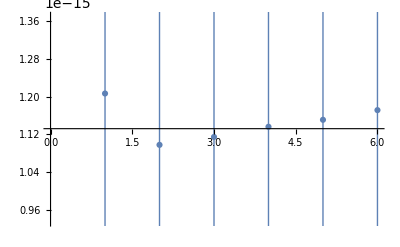
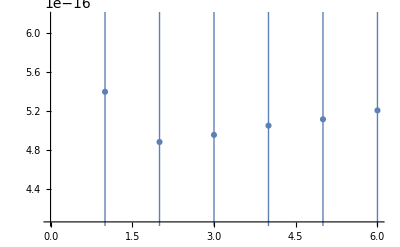
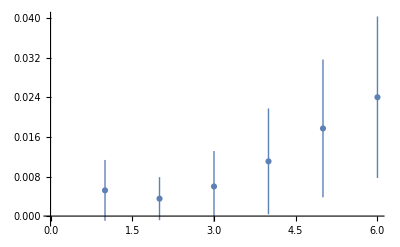
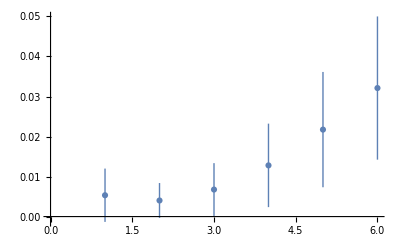
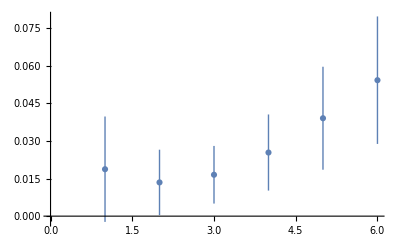
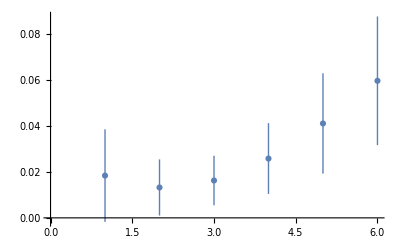
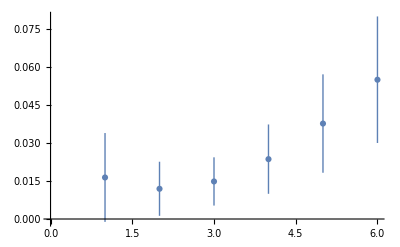
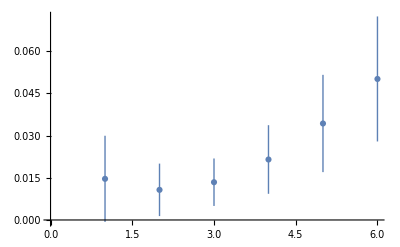

```mathematica
Table[ListPlot[Table[Around[Table[aa[[z]][[x]][[y]],{x,100}]],{y,6}]],{z,Dimensions[aa][[1]]}]
```

```mathematica
Table[Count[Flatten[Table[Position[aa[[z]][[x]],Min[aa[[z]][[x]]]],{x,100}]],2],{z,Dimensions[aa][[1]]}]
```

{5,5,33,26,29,27,29,29,37,30,47,63,65,65,69,76,70,64,70,69,68,68,68,66,70,70,71,70,71,71}

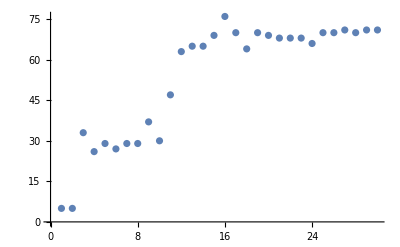

```mathematica
ListPlot[{5,5,33,26,29,27,29,29,37,30,47,63,65,65,69,76,70,64,70,69,68,68,68,66,70,70,71,70,71,71}]
```

```mathematica
N[1/12]
```

0.0833333